```mathematica
solutions:={{t->(-1+x^2+y^2+z1-x z1-z1 √(1+y^2-z1+x (-2+x+z1)))/(2 (-1+x))},{t->(-1+x^2+y^2+z1-x z1+z1 √(1+y^2-z1+x (-2+x+z1)))/(2 (-1+x))}}/.{z1->Sqrt[(x-1)^2+y^2]}
t/.solutions[[1]]
```

1/(2 (-1+x))(-1+x^2+y^2+√((-1+x)^2+y^2)-x √((-1+x)^2+y^2)-√((-1+x)^2+y^2) √(1+y^2-√((-1+x)^2+y^2)+x (-2+x+√((-1+x)^2+y^2))))

Part::pkspec1: The expression num cannot be used as a part specification.

ReplaceAll::reps: {solutions⟦num⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
worstT:=Function[{xx,yy},Piecewise[{
{1-3Abs[yy]/4,xx==1},
{(t/.solutions⟦1⟧)/.{x->xx,y->yy},True}
}]]
```

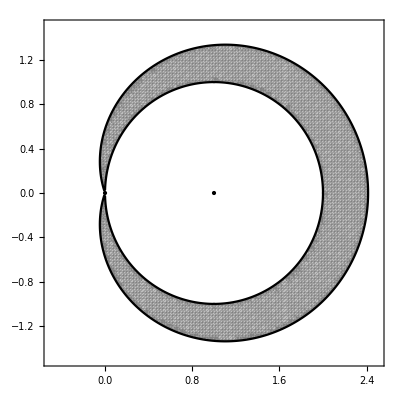

```mathematica
plot =Show[
RegionPlot[
{worstT[x,y]>0&&(x-1)^2+y^2>1},
{x,-1/2,3-1/2},
{y,-3/2,3/2},
PlotStyle->Directive[GrayLevel[0.5],Opacity[0.5]],(*Gray with 50% opacity*)
BoundaryStyle->Black (*Black border*),
PlotPoints->100
],
(*Graphics[{Dashed,Circle[{1,0},1]}],*)
Graphics[{PointSize[Large],Point[{0,0}],Point[{1,0}]}]
]
```

```mathematica
Export[StringJoin[{NotebookDirectory[],"figure_2.2.png"},""],plot]
```

C:\Users\jared\Dropbox\Pony Express\Faulty Delivery\Mathematica\for_paper\